# CRISPR : Experiment 3

## [ρ,Ν] to P_(extermination)

## Parameters and Functions Definition

```mathematica
namingScalingFactor=1000000000000;
CalculateRepetitionQuartiles[individualRepetition_]:=Map[Quartiles,Transpose/@Transpose[individualRepetition],{2}]
PlotQuartilesTiming[quartilesData_,title_]:=Module[{dynamics},
dynamics=Table[
ListLinePlot[
{quartilesData[[i,1]],quartilesData[[i,3]],quartilesData[[i,2]]},
PlotStyle->{{colors[[2,i]]},{colors[[2,i]]},{Thickness[.0075],colors[[1,i]]}},
Filling->{1->{2}},
PlotRange->All,
InterpolationOrder->1
]
,{i,1,quartilesData//Length}];
Show[dynamics,
PlotRange->All,
BaseStyle->20,(*FrameLabel->{"Time","PopulationSize"},*)
Frame->True,
GridLines->Automatic(*{Range[0,1000000,100],Range[0,1000000,1000]}*),
ImageSize->800,
FrameStyle->Directive[Gray,Thick],
GridLinesStyle->Directive[Dashed,Thin]
(*PlotLabel->("[ρ: "<>ToString[EngineeringForm[title[[1]]/namingScalingFactor]]<>", N: "<>ToString[title[[4]]/namingScalingFactor]<>"]")*)]
]
colorsStrings={"Cyan","Blue","Green","Purple","Yellow","Orange","Red"};
lightColorStrings=StringJoin["Light",#]&/@colorsStrings;
colors={ToExpression/@colorsStrings,ToExpression/@lightColorStrings};
colors=ColorData[1,"ColorList"];
{frame,frameTicksStyle,baseStyle,frameStyle,imageSize,aspectRatio,gridLinesStyle,thicknessLow,thicknessHigh}={True,15,25,Directive[Gray,Thick],500,1,Directive[Gray,Thin,Dashed],.001,.0075};
```

## Load Data

{35559,186}

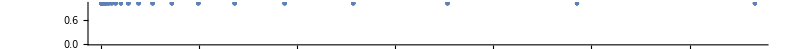
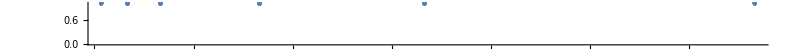
ρ: | -Graphics-
Ν: | -Graphics-

```mathematica
(*LoadFolder*)
SetDirectory[NotebookDirectory[]];
csvNames=FileNames["*.csv","./Data/"];
(*GetSortedCoordinates*)
csvCoords=Map[ToExpression,(StringSplit[#,{"/","_"}]&/@csvNames)[[All,3;;6]],Infinity];
ordering=Ordering[csvCoords];
csvCoords=csvCoords[[ordering]];
(*GetSortedIdentifiers*)
csvIdentifiers=(csvCoords//DeleteDuplicates);
(*GetSortedData*)
csvData=ParallelMap[Import[#]&,csvNames];
csvData=csvData[[ordering]];
(*GetSortedRepetitions*)
repetitionsIndexes=Flatten[Position[csvCoords,#]]&/@csvIdentifiers;
repetitionsData=(csvData[[#]]&/@repetitionsIndexes);
(*Statistics*)
{csvNames//Length,csvIdentifiers//Length}
rhoResolution=DeleteDuplicates[csvCoords[[All,1]]]//Length;
popResolution=DeleteDuplicates[csvCoords[[All,4]]]//Length;
rhoDensityPlot=NumberLinePlot[(csvIdentifiers/namingScalingFactor//N)[[All,1]],ImageSize->800];
popDensityPlot=NumberLinePlot[(csvIdentifiers/namingScalingFactor//N)[[All,4]],ImageSize->800];
densities=Grid[{
{"ρ:",rhoDensityPlot},
{"Ν:",popDensityPlot}
}]
```

```mathematica
Export["sampledDensitiesGrid.eps",densities]
```

sampledDensitiesGrid.eps

```mathematica
popSizes=DeleteDuplicates[csvCoords[[All,4]]]/namingScalingFactor
Directory[]
```

{1000,5000,10000,25000,50000,100000}

/Users/sanchez.hmsc/Downloads/CRISPRCAS9-master/02RevisedDatasets/Experiment03

```mathematica
Length/@repetitionsIndexes
rhoResolution
```

{149,199,197,197,196,164,197,196,197,197,197,164,197,197,196,197,197,164,198,200,197,197,196,164,196,197,196,198,196,164,196,197,196,196,196,165,197,196,198,196,196,164,196,197,197,196,196,165,196,198,196,196,196,165,196,198,197,196,196,164,197,196,197,197,196,164,201,196,196,198,197,164,196,197,196,196,198,165,197,197,196,198,197,164,198,198,196,197,197,164,196,197,197,196,197,166,196,197,198,196,197,165,197,196,196,196,198,164,196,196,197,196,197,164,199,198,196,196,196,165,197,198,197,196,196,166,196,196,196,196,196,164,196,197,197,198,196,164,198,197,197,197,197,164,196,198,197,197,199,165,197,196,196,196,196,165,199,197,198,196,196,167,197,196,200,196,196,165,198,197,196,197,198,164,196,196,196,200,199,164,196,196,198,196,197,164}

31

## Elimination Probabilities

### Probabilities Calculation

```mathematica
indexOfInterest=7;
(*------------------*)
eliminationBoolRepetitions=Table[
(**)
initPops=First/@repetitionsData[[i]][[All,indexOfInterest]];
lastPops=Last/@repetitionsData[[i]][[All,indexOfInterest]];
(**)
eliminationBool=If[#==0,1,0]&/@(lastPops)//N
,{i,1,repetitionsData//Length}];
(*------------------*)
meanEliminationProbabilities=Mean/@eliminationBoolRepetitions;
(*------------------*)
dataTuples={csvIdentifiers,meanEliminationProbabilities}//Transpose;
dataPointsFlat=Flatten/@({#[[1]]/namingScalingFactor,#[[2]]}&/@dataTuples//N);
```

### Raw Data Curves

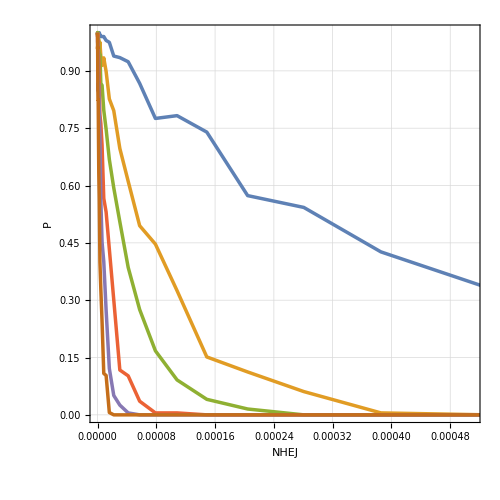
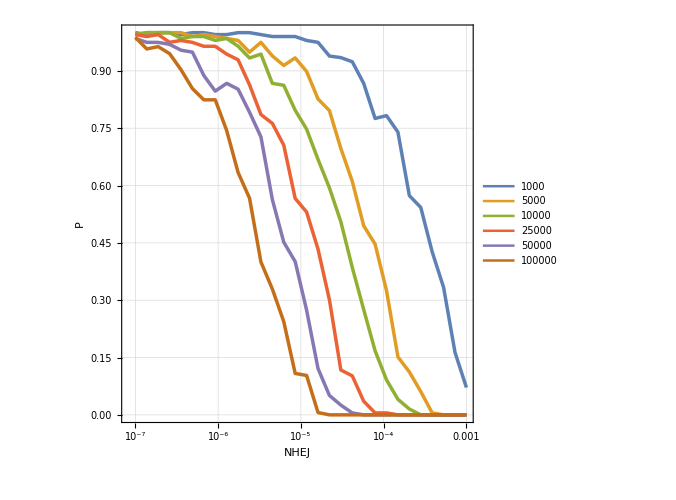
-Graphics- | -Graphics-

```mathematica
(*Getting Dataset*)
indVectors=dataTuples[[All,1,4]]//DeleteDuplicates;
data=Table[
dataset=Cases[dataTuples,{{rho_,Floor[.99*namingScalingFactor],0,indVectors[[i]]},out_}->N[{rho/namingScalingFactor,out}]]
,{i,1,indVectors//Length}];
(*Lin and Log data plots*)
crashProbLinLinData=ListPlot[data
(*,PlotLegends->(indVectors/namingScalingFactor)*)
,PlotStyle->Thickness[.005]
,Frame->frame
,Joined->True
,FrameTicksStyle->frameTicksStyle
,FrameLabel->{"NHEJ","P"}
,BaseStyle->baseStyle
,GridLines->Automatic
,FrameStyle->frameStyle
,GridLinesStyle->gridLinesStyle
,ImageSize->imageSize
,AspectRatio->aspectRatio
];
crashProbLogLinData=ListLogLinearPlot[data
,PlotLegends->(indVectors/namingScalingFactor)
,PlotStyle->Thickness[.005]
,Frame->frame
,Joined->True
,FrameTicksStyle->frameTicksStyle
,FrameLabel->{"NHEJ","P"}
,BaseStyle->baseStyle
,GridLines->Automatic
,FrameStyle->frameStyle
,GridLinesStyle->gridLinesStyle
,ImageSize->imageSize
,AspectRatio->aspectRatio
];
(*Grid*)
Grid[{{crashProbLinLinData,crashProbLogLinData}}]
```

### Elimination Curves Fits

#### Log

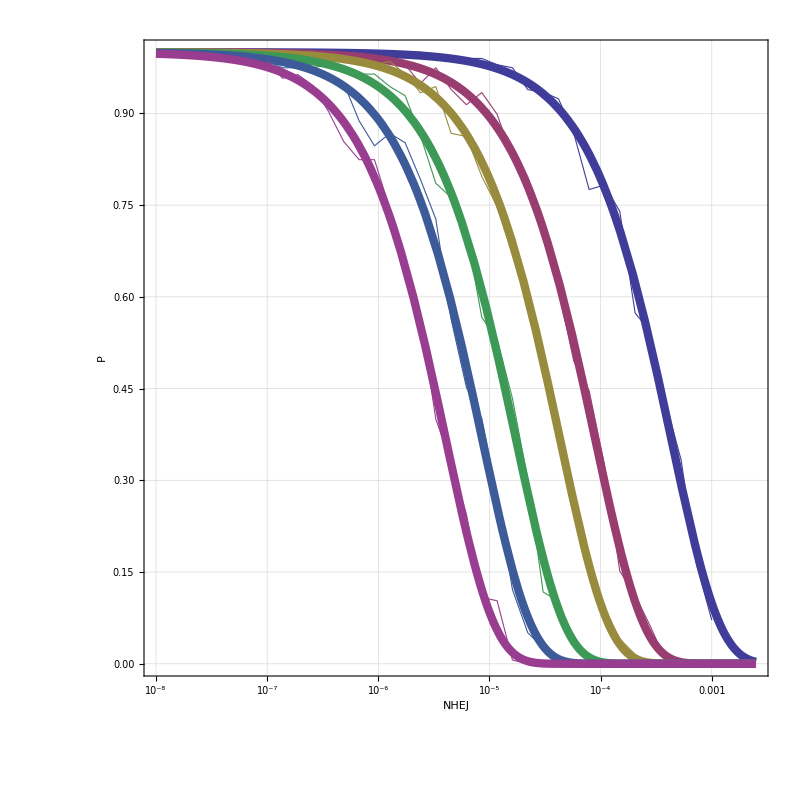
-Graphics- |

NHEJLog.eps

```mathematica
(*Fit Data to Prototype Function*)
prototypeFunction[x_,k_,c_]:=ⅇ^(-k*x)
fits=Table[
nlm=NonlinearModelFit[data[[i]],prototypeFunction[x,k,c],{k,c},x];
{
Show[
LogLinearPlot[
nlm[x]
,{x,.00000001,.0025}
,PlotStyle->{{Thickness[.0075],colors[[i]]}}
],
ListLogLinearPlot[data[[i]],PlotStyle->{{Opacity[1],Thickness[.001],PointSize[.01],colors[[i]]}},Joined->True]
,Frame->True
,FrameTicksStyle->15
,FrameLabel->{"NHEJ","P"}
,BaseStyle->25
,GridLines->Automatic
,FrameStyle->Directive[Gray,Thick]
,GridLinesStyle->Directive[Gray,Thin,Dashed]
,ImageSize->imageSize
,AspectRatio->1
]
,nlm//Normal
,nlm
}
,{i,1,data//Length}];
popLogFitsNormal=fits[[All,2]];
(*legends=StringJoin@@@Transpose[{ToString/@(indVectors/namingScalingFactor),ConstantArray[" :: [",Length[indVectors]],ToString/@StandardForm/@popLogFitsNormal,ConstantArray["]",Length[indVectors/namingScalingFactor]]}]*)
legends=ToString/@(indVectors/namingScalingFactor);
logFits=Grid[{{
fits[[All,1]]//Show[#,ImageSize->800,PlotLegends->Automatic]&,
LineLegend[colors,legends,LegendLabel->"N",LabelStyle->Directive[Thick,Gray,20]](*LineLegend[colors,legends,LegendLabel->"N :: [Exponential Decay]",LabelStyle->Directive[Thick,Gray,20]]*)
}}]
Export["NHEJLog.eps",logFits,ImageSize->1000]
```

#### Lin

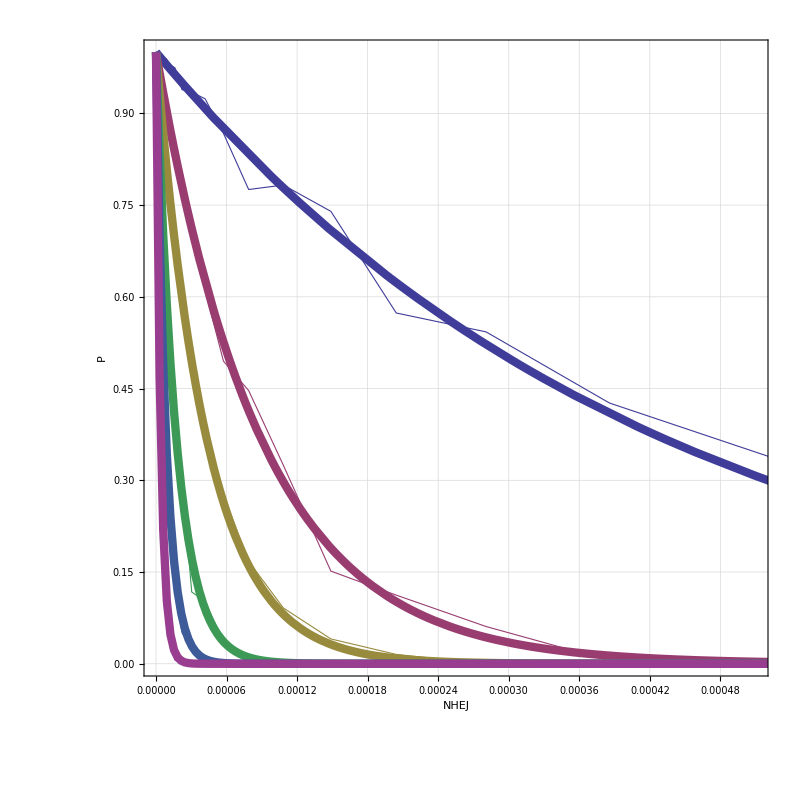

NHEJLinear.eps

```mathematica
functions=fits[[All,2]];
listLineProbabilitiesPlots=ListPlot[data
,PlotStyle->Table[{Thickness[thicknessLow],i},{i,colors}]
,Frame->frame
,Joined->True
,FrameTicksStyle->frameTicksStyle
,FrameLabel->{"NHEJ","P"}
,BaseStyle->baseStyle
,GridLines->Automatic
,FrameStyle->frameStyle
,GridLinesStyle->gridLinesStyle
,ImageSize->800
,AspectRatio->aspectRatio
];
fitProbabilitiesPlots=Table[
Plot[functions[[i]],{x,0,.01}
,PlotRange->{0,1}
,PlotStyle->{Thickness[thicknessHigh],colors[[i]]}
,PlotRange->{-1,1}
],{i,1,data//Length}]//Show[#]&;
linFits=Show[Flatten[{listLineProbabilitiesPlots,fitProbabilitiesPlots}]]
Export["NHEJLinear.eps",linFits,ImageSize->1000]
(*functions=fits[[All,2]];
fitsPlot=Plot[functions,{x,0,.001},PlotRange->{0,1},PlotLegends->Automatic,PlotStyle->{Thickness[thicknessHigh],colors}];
fitsAndPoints=Show[{listLineProbabilitiesPlots,fitsPlot}]*)
```

### Grid

```mathematica
Grid[{{linFits,logFits}}]
```

-Graphics- | -Graphics- |

### Breaking Points Calculations

#### Linear

```mathematica
confidence={.5,.75,.85,.9,.99};
breakingPoints=Table[Solve[fits[[All,2]][[i]]==#,x][[1,1,2]]//Quiet,{i,1,Length[fits]}]&/@confidence;
popCoords=Transpose[{popSizes,#}]&/@breakingPoints;
popSizeRho=ListLinePlot[popCoords
,PlotStyle->Table[{Thickness[thicknessHigh],i},{i,colors}]
,Frame->frame
,Joined->True
,InterpolationOrder->1
,FrameTicksStyle->frameTicksStyle
,FrameLabel->{"N","NHEJ"}
,BaseStyle->baseStyle
,GridLines->Automatic
,FrameStyle->frameStyle
,GridLinesStyle->gridLinesStyle
,ImageSize->800
,AspectRatio->aspectRatio]
Export["NHEJCriticalLinear.eps",popSizeRho,ImageSize->1000]
```

Transpose::nmtx: The first two levels of {popSizes,{0.000299578,0.0000619146,0.0000298666,0.0000119879,5.95928×10^-6,2.80155×10^-6}} cannot be transposed.

Transpose::nmtx: The first two levels of {popSizes,{0.000124336,0.0000256969,0.0000123958,4.97543×10^-6,2.47333×10^-6,1.16275×10^-6}} cannot be transposed.

Transpose::nmtx: The first two levels of {popSizes,{0.0000702407,0.0000145168,7.00268×10^-6,2.81074×10^-6,1.39724×10^-6,6.56867×10^-7}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

-Graphics-

NHEJCriticalLinear.eps

#### Inverse

```mathematica
breakingPoints=Table[Solve[fits[[All,2]][[i]]==#,x][[1,1,2]]//Quiet,{i,1,Length[fits]}]&/@confidence;
popCoords=Transpose[{1/popSizes,#}]&/@breakingPoints;
popSizeRhoInv=ListLinePlot[popCoords
,PlotStyle->Table[{Thickness[thicknessLow],i},{i,colors}]
,Frame->frame
,Joined->True
,InterpolationOrder->1
,FrameTicksStyle->frameTicksStyle
,FrameLabel->{"1/N","NHEJ"}
,BaseStyle->baseStyle
,GridLines->Automatic
,FrameStyle->frameStyle
,GridLinesStyle->gridLinesStyle
,ImageSize->800
,AspectRatio->aspectRatio
,PlotRange->All
];
popSizeRhoInvLeg=Grid[{{
popSizeRhoInv,
LineLegend[colors,confidence,LegendLabel->"Crash Confidence",LabelStyle->Directive[Thick,Gray,20]]
}}]
```

Transpose::nmtx: The first two levels of {1/popSizes,{0.000299578,0.0000619146,0.0000298666,0.0000119879,5.95928×10^-6,2.80155×10^-6}} cannot be transposed.

Transpose::nmtx: The first two levels of {1/popSizes,{0.000124336,0.0000256969,0.0000123958,4.97543×10^-6,2.47333×10^-6,1.16275×10^-6}} cannot be transposed.

Transpose::nmtx: The first two levels of {1/popSizes,{0.0000702407,0.0000145168,7.00268×10^-6,2.81074×10^-6,1.39724×10^-6,6.56867×10^-7}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

-Graphics- |

#### Linear (Inverse) Fits

```mathematica
popLinearFits=NonlinearModelFit[#,m*x,{m,c},x]&/@popCoords;
popLinearFitsNormal=Normal/@popLinearFits
fitProbabilitiesPlots=Table[
Plot[
Callout[popLinearFits[[i]]//Normal,StringReplace[ToString[popLinearFitsNormal[[i]]],"x"->"1/N"],Top,LabelStyle->Directive[12.5,Gray],LeaderSize->10,Appearance->"None",CalloutMarker->"CirclePoint",Background->Directive[White,Opacity[0]]]
,{x,0,.001}
,PlotStyle->{Thickness[thicknessHigh],colors[[i]]}
,Frame->frame
,FrameTicksStyle->frameTicksStyle
,FrameLabel->{"1/N","NHEJ"}
,BaseStyle->baseStyle
,GridLines->Automatic
,FrameStyle->frameStyle
,GridLinesStyle->gridLinesStyle
,ImageSize->800
,AspectRatio->aspectRatio
],{i,1,popLinearFits//Length}]//Show
(*legends=StringJoin@@@Transpose[{ToString/@confidence,ConstantArray[" :: [",Length[confidence]],ToString/@StandardForm/@popLinearFitsNormal,ConstantArray["]",Length[confidence]]}]*)
legends=ToString/@confidence;
```

NonlinearModelFit::fitd: First argument Transpose[{1/popSizes,{0.000299578,0.0000619146,0.0000298666,0.0000119879,5.95928×10^-6,2.80155×10^-6}}] in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit::fitd: First argument Transpose[{1/popSizes,{0.000124336,0.0000256969,0.0000123958,4.97543×10^-6,2.47333×10^-6,1.16275×10^-6}}] in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit::fitd: First argument Transpose[{1/popSizes,{0.0000702407,0.0000145168,7.00268×10^-6,2.81074×10^-6,1.39724×10^-6,6.56867×10^-7}}] in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument Transpose[{1/popSizes,{0.000299578,0.0000619146,0.0000298666,0.0000119879,5.95928×10^-6,2.80155×10^-6}}] in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit::fitd: First argument Transpose[{1/popSizes,{0.000124336,0.0000256969,0.0000123958,4.97543×10^-6,2.47333×10^-6,1.16275×10^-6}}] in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit::fitd: First argument Transpose[{1/popSizes,{0.0000702407,0.0000145168,7.00268×10^-6,2.81074×10^-6,1.39724×10^-6,6.56867×10^-7}}] in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

{NonlinearModelFit[Transpose[{1/popSizes,{0.000299578,0.0000619146,0.0000298666,0.0000119879,5.95928×10^-6,2.80155×10^-6}}],m x,{m,c},x],NonlinearModelFit[Transpose[{1/popSizes,{0.000124336,0.0000256969,0.0000123958,4.97543×10^-6,2.47333×10^-6,1.16275×10^-6}}],m x,{m,c},x],NonlinearModelFit[Transpose[{1/popSizes,{0.0000702407,0.0000145168,7.00268×10^-6,2.81074×10^-6,1.39724×10^-6,6.56867×10^-7}}],m x,{m,c},x],NonlinearModelFit[Transpose[{1/popSizes,{0.0000455369,9.41121×10^-6,4.53982×10^-6,1.8222×10^-6,9.0583×10^-7,4.25845×10^-7}}],m x,{m,c},x],NonlinearModelFit[Transpose[{1/popSizes,{4.34376×10^-6,8.97735×10^-7,4.33053×10^-7,1.73819×10^-7,8.6407×10^-8,4.06213×10^-8}}],m x,{m,c},x]}

NonlinearModelFit::fitd: First argument Transpose[{1/popSizes,{0.000299578,0.0000619146,0.0000298666,0.0000119879,5.95928×10^-6,2.80155×10^-6}}] in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit::fitd: First argument Transpose[{1/popSizes,{0.000124336,0.0000256969,0.0000123958,4.97543×10^-6,2.47333×10^-6,1.16275×10^-6}}] in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit::fitd: First argument Transpose[{1/popSizes,{0.0000702407,0.0000145168,7.00268×10^-6,2.81074×10^-6,1.39724×10^-6,6.56867×10^-7}}] in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

General::ivar: 2.04286×10^-8 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Max::nord: Invalid comparison with ComplexInfinity attempted.

Divide::indet: Indeterminate expression 0./0. encountered.

Range::range: Range specification in Range[0.,0.,0.] does not have appropriate bounds.

Divide::indet: Indeterminate expression 0./0. encountered.

Range::range: Range specification in Range[0.,0.,0.] does not have appropriate bounds.

Divide::indet: Indeterminate expression 0./0. encountered.

General::stop: Further output of Divide::indet will be suppressed during this calculation.

Range::range: Range specification in Range[0.,0.,0.] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Max::nord: Invalid comparison with ComplexInfinity attempted.

Divide::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Transpose::nmtx: The first two levels of {{},Indeterminate} cannot be transposed.

Transpose::nmtx: The first two levels of {Range[0.,0.,0.],Range[0.,0.,0.]} cannot be transposed.

MapThread::mptd: Object Transpose[{Range[0.,0.,0.],Range[0.,0.,0.]}] at position {2, 1} in MapThread[Rescale[#1,#2]&,{Transpose[{Range[0.,0.,0.],Range[0.,0.,0.]}],{{0.,0.},{-0.05,0.05}}}] has only 0 of required 1 dimensions.

RegionNearest::regp: A correctly specified region expected at position 1 of RegionNearest[Line[Transpose[MapThread[Rescale[#1,#2]&,{Transpose[{Range[«3»],Range[«3»]}],{{0.,0.},{-0.05,0.05}}}]]],{0.,0.}].

MapThread::mptd: Object RegionNearest[Line[Transpose[MapThread[Rescale[#1,#2]&,{Transpose[{Range[«3»],Range[«3»]}],{{0.,0.},{-0.05,0.05}}}]]],{0.,0.}] at position {2, 1} in MapThread[Rescale[#1,{0,1},#2]&,{RegionNearest[Line[Transpose[MapThread[Rescale[«2»]&,{Transpose[«1»],{«2»}}]]],{0.,0.}],{{0.,0.},{-0.05,0.05}}}] has only 0 of required 1 dimensions.

Transpose::nmtx: The first two levels of {Interpolation[Transpose[{{},Indeterminate}],InterpolationOrder→1][0],Interpolation[Transpose[{{},Indeterminate}],InterpolationOrder→1][0.],Interpolation[Transpose[{{},Indeterminate}],InterpolationOrder→1][0.268438]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

MapThread::mptd: Object Transpose[{Interpolation[Transpose[{{},Indeterminate}],InterpolationOrder→1][0],Interpolation[Transpose[{{},Indeterminate}],InterpolationOrder→1][0.],Interpolation[Transpose[{{},Indeterminate}],InterpolationOrder→1][0.268438]}] at position {2, 1} in MapThread[Rescale[#1,#2]&,{Transpose[{Interpolation[Transpose[{{},Indeterminate}],InterpolationOrder→1][0],Interpolation[Transpose[{{},Indeterminate}],InterpolationOrder→1][0.],Interpolation[Transpose[{{},Indeterminate}],InterpolationOrder→1][0.268438]}],{{-0.00116575,0.0010442},{-0.0555556,1.05556}}}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::partw: Part 2 of Interpolation[{{0.,Range[0.,0.,0.]},{0.,Range[0.,0.,0.]}},InterpolationOrder→1][0.] does not exist.

Interpolation::innd: First argument in Transpose[{{},Indeterminate}] does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

Interpolation::inord: Value of option InterpolationOrder -> 1. should be a non-negative machine-sized integer or a list of integers with length equal to the number of dimensions, 1.

Part::partw: Part 2 of Interpolation[{{0.,Range[0.,0.,0.]},{0.,Range[0.,0.,0.]}},InterpolationOrder→1.][0.] does not exist.

Max::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Divide::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

RegionNearest::regp: A correctly specified region expected at position 1 of RegionNearest[Line[Transpose[MapThread[Rescale[#1,#2]&,{Transpose[{Range[«3»],Range[«3»]}],{{0.,0.},{-0.05,0.05}}}]]],{0.,0.}].

Part::partw: Part 2 of Interpolation[{{0.,Range[0.,0.,0.]},{0.,Range[0.,0.,0.]}},InterpolationOrder→1][0.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::inord: Value of option InterpolationOrder -> 1. should be a non-negative machine-sized integer or a list of integers with length equal to the number of dimensions, 1.

Divide::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

RegionNearest::regp: A correctly specified region expected at position 1 of RegionNearest[Line[Transpose[MapThread[Rescale[#1,#2]&,{Transpose[{Range[«3»],Range[«3»]}],{{0.,0.},{-0.05,0.05}}}]]],{0.,0.}].

General::stop: Further output of RegionNearest::regp will be suppressed during this calculation.

Interpolation::inord: Value of option InterpolationOrder -> 1. should be a non-negative machine-sized integer or a list of integers with length equal to the number of dimensions, 1.

General::stop: Further output of Interpolation::inord will be suppressed during this calculation.

-Graphics-

```mathematica
linearFitsPlots=Grid[{{
Show[fitProbabilitiesPlots,popSizeRhoInv,ImagePadding->All],
LineLegend[colors,legends,LegendLabel->"Crash Confidence",LabelStyle->Directive[Thick,Gray,20]]
(*LineLegend[colors,legends,LegendLabel->"Crash Confidence :: [Linear Regression]",LabelStyle->Directive[Thick,Gray,20]]}*)
}}]
Export["NHEJCriticalLog.eps",linearFitsPlots,ImageSize->1000]
```

-Graphics- |

NHEJCriticalLog.eps

### Full Grid

```mathematica
fullGrid=Grid[{
{linFits,logFits},
{popSizeRho,linearFitsPlots}
}
,Frame->{None,{True,True}}
,FrameStyle->Directive[Thick,Gray,Dashed]
]
Export["grid.eps",fullGrid]
```

-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |

grid.eps

## Time-Dependent Dynamics

### All

```mathematica
plots=Table[
{rhoValue,eValue,sValue,nValue}=csvIdentifiers[[i]];
i=Position[csvIdentifiers,{rhoValue,eValue,sValue,nValue}][[1,1]];
individualRepetition=repetitionsData[[i]];
quartilesData=Transpose/@CalculateRepetitionQuartiles[individualRepetition];
PlotQuartilesTiming[quartilesData,csvIdentifiers[[i]]//N]
,{i,1,csvIdentifiers//Length}];
```

Part::partw: Part 4 of RGBColor[0.6, 0.24, 0.4428931686004542] does not exist.

Part::partw: Part 4 of RGBColor[0.24720000000000014, 0.24, 0.6] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

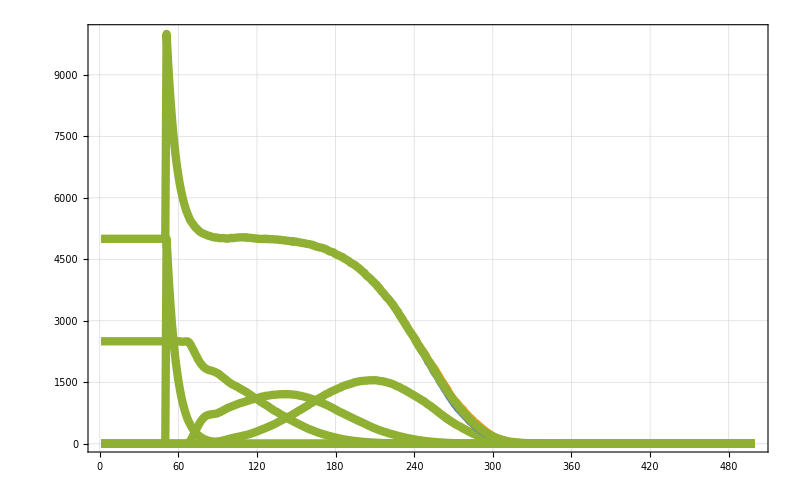

```mathematica
plots[[2]]
```

### Plot Grid Timed

```mathematica
colorsStrings={"Cyan","Blue","Green","Purple","Yellow","Orange","Red"};
lightColorStrings=StringJoin["Light",#]&/@colorsStrings;
colors={ToExpression/@colorsStrings,ToExpression/@lightColorStrings};
(**)
plots=Table[
{rhoValue,eValue,sValue,nValue}=csvIdentifiers[[i]];
i=Position[csvIdentifiers,{rhoValue,eValue,sValue,nValue}][[1,1]];
individualRepetition=repetitionsData[[i]];
quartilesData=Transpose/@CalculateRepetitionQuartiles[individualRepetition];
PlotQuartilesTiming[quartilesData,csvIdentifiers[[i]]//N]//Show[#]&
,{i,1,csvIdentifiers//Length}];
```

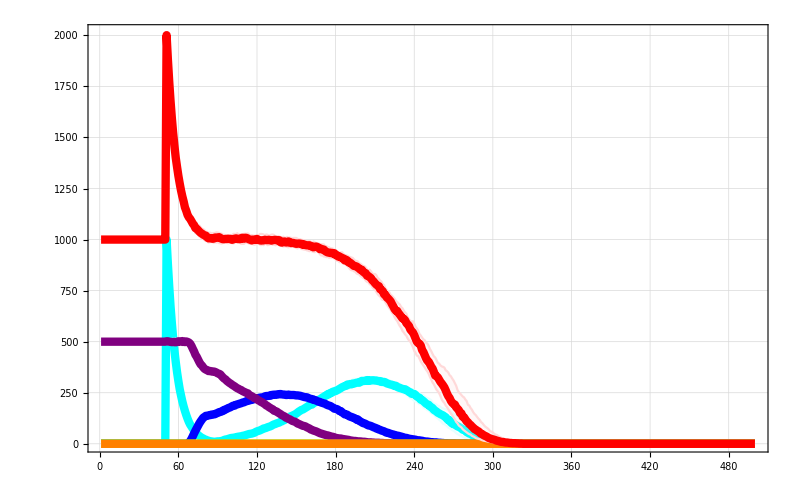
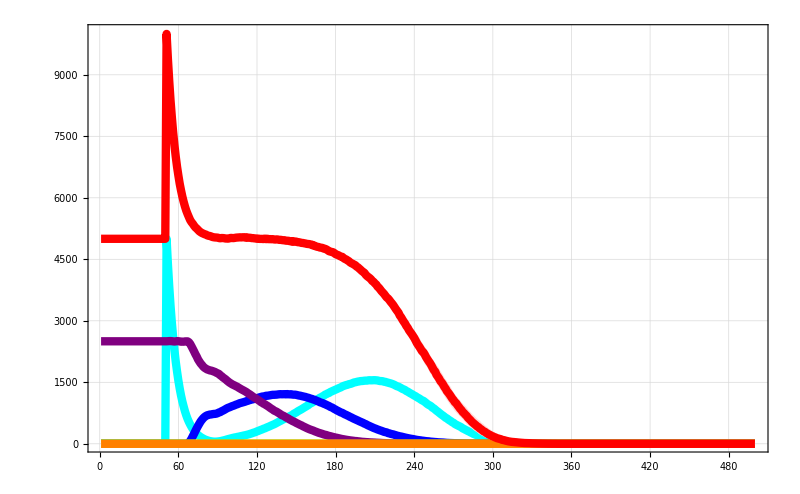
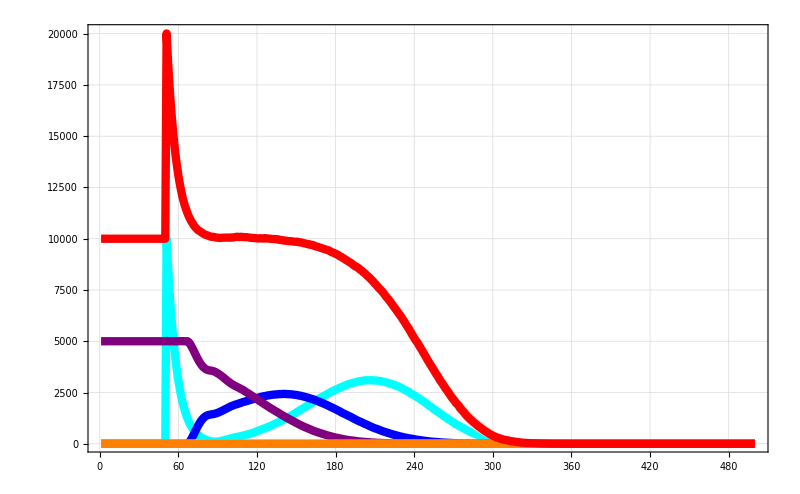
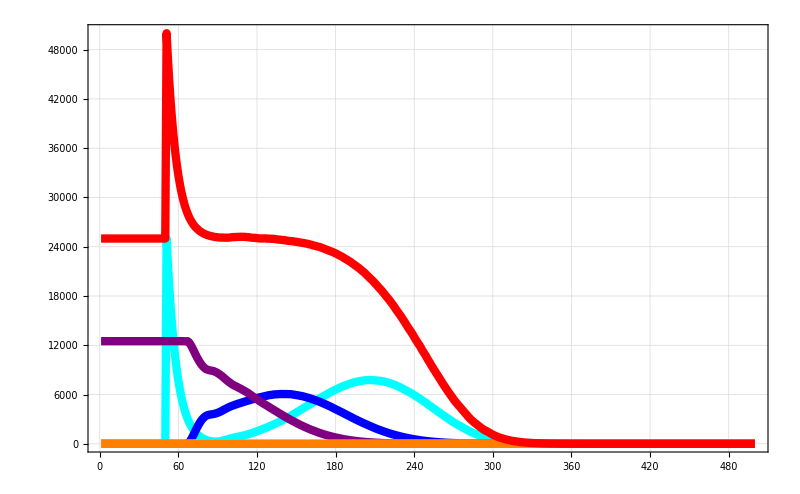
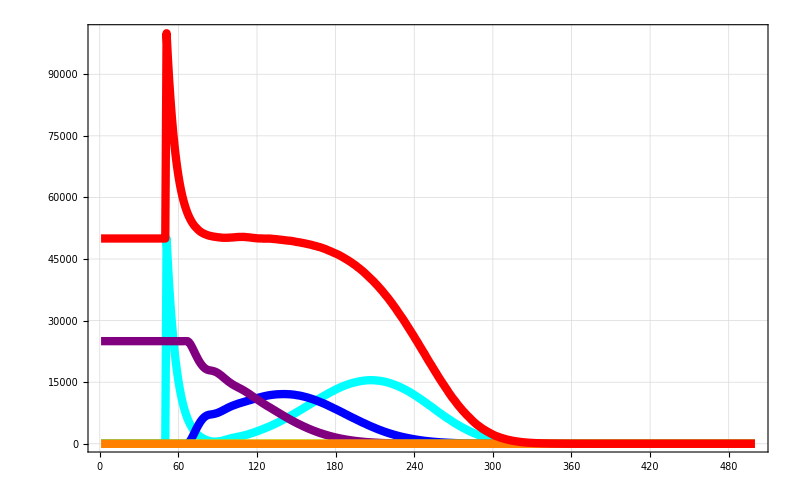
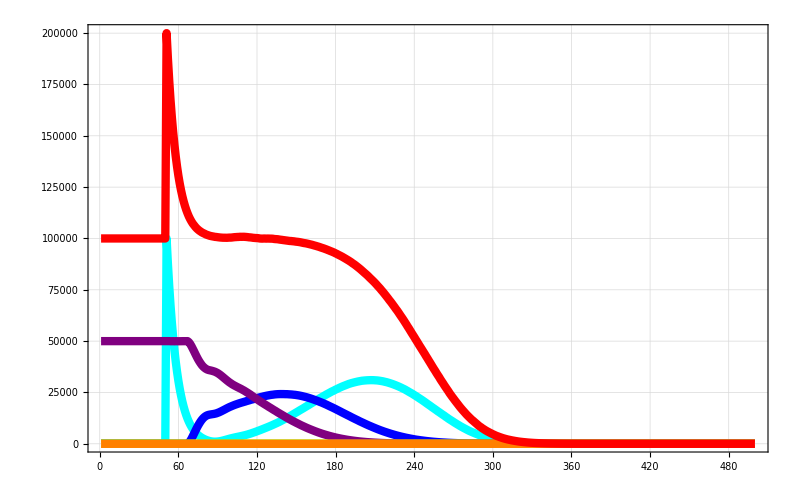
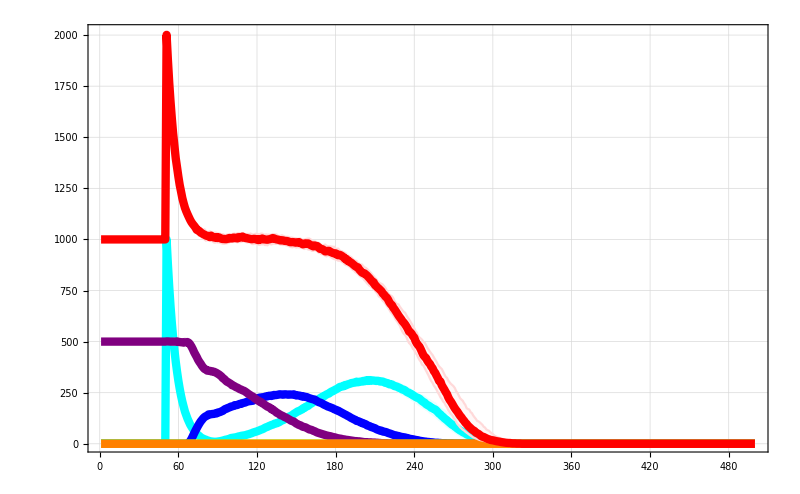
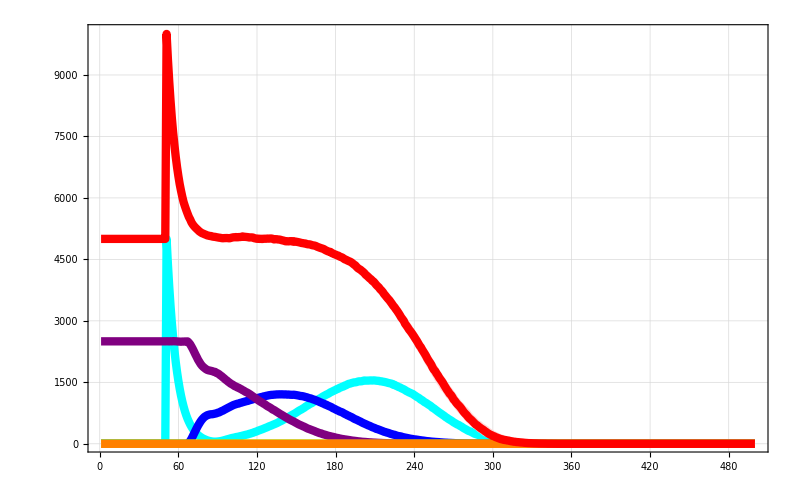
ρ\Ν | 1000 | 5000 | 10000 | 25000 | 50000 | 100000
0. | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
3.56224×10^-7 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1.74333×10^-6 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
8.53168×10^-6 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.0000417532 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.000204336 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.001 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
plotsGrid=Table[
plots[[(i*popResolution)+1;;(i*popResolution)+popResolution]]
,{i,0,rhoResolution-1}];
plotsGrid=Prepend[Transpose[plotsGrid],Rotate[ToString[TraditionalForm[Style[#,20]]],90Degree]&/@(DeleteDuplicates[csvCoords[[All,1]]]/namingScalingFactor//N)]//Transpose;
outGrid=plotsGrid[[#]]&/@Range[1,plotsGrid//Length,5]//Grid[
Prepend[#,Flatten[{Style["ρ\Ν",Bold,30],ToString[TraditionalForm[Style[#,20]]]&/@(DeleteDuplicates[csvCoords[[All,4]]]/namingScalingFactor)}]]
,Background->{{LightBlue},{LightBlue}},Frame->All]&
```

```mathematica
Export["gridTime.png",outGrid]
```

gridTime.png